-Graphics-

Bienvenidos a mmAeScience!
https://github.com/josemramirez/mmaescience /QM_intro-[for MMaTeX]_beta^v14

# eScience - Habla Mecánica Cuántica!

Funciones:

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"QMfunctions_v1.nb"];
```

```mathematica
Siguiendo la segunda edición de David J Griffiths, Reed College.
por JM Ramírez, 2024.
```

```mathematica
PARTE I Teoría
```

◀ prev - + prox ▶

e Guardar
d Resetear

## Capítulo 1: La función de onda

◀ prev - + prox ▶

e Guardar
d Resetear

## El programa de Mecánica Clásica:

```mathematica
Se trata de determinar x(t) ⇒ "esta es la cantidad de estrellas, ¡se llama trayectoria!". ¿Cómo encontramos la trayectoria?
bueno, usando Newton:
```

-(∂V)/(∂x)= m (dx(t))/dt

◀ prev - + prox ▶

e Guardar
d Resetear

La ecuación de Schrödinger

Buscamos la función de onda de la partícula, Ψ(x,t), y la obtenemos resolviendo la ecuación de Schrödinger:

ⅈℏ(∂Ψ)/(∂t)=-ℏ^2/(2m)(∂^2 Ψ)/(∂x^2)+VΨ     (1.1)

```mathematica
Ψ = Ψ(x,t): función de onda; V = V(x,t): función de energía potencial; m = masa de partículas.
```

◀ prev - + prox ▶

e Guardar
d Resetear

La interpretación estadística

```mathematica
La interpretación estadística de Born de la función de onda, que dice que |Ψ(x,t)|^2 da la probabilidad de encontrar la partícula en el punto x, en el tiempo t, o más precisamente,
```

∫_a^b |Ψ(x,t)|^2 ⅆx≡
Probabilidad de hallar a la particula entre a y b en el tiempo t.     (1.3)

```mathematica
myPDF = PDF[NormalDistribution[0, 1], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

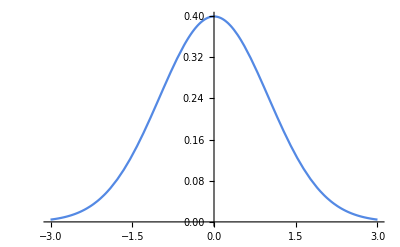

```mathematica
Plot[myPDF, {x, -3, 3}]
```

```mathematica
myProba1 = Integrate[myPDF, {x, 0.5, 1.}]
```

0.149882

15%! ... continuar...

```mathematica
myPDF4Fig12 = (PDF[NormalDistribution[0, 1], x] Sin[2.6 x + 1.5])^2
```

(ⅇ^(-x^2) Sin[1.5+2.6 x]^2)/(2 π)

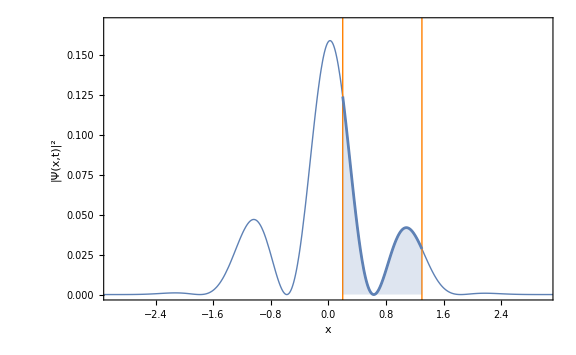

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
a1=0.2;
b1=1.3;
(* == 1ro sin refilear === *)
PnFil1=Plot[{myPDF4Fig12},{x,-4,4},
Epilog->{Orange,Line[{{a1,-5},{a1,16}}],Line[{{b1,-5},{b1,16}}]},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,20],
FrameLabel->{Style["x",24],
Style["|Ψ(x,t)|^2",24],"Fig 1.2: A typical wave function"},
PlotStyle->Thick,FrameTicks->None,
PlotRange->{{-3,3},{0,0.17}},
ImageSize->Large];
(* == Ahora refilear === *)
PnFil2=Plot[{myPDF4Fig12},{x,a1,b1},
Filling->Axis];
Show[PnFil1,PnFil2]
```

Probabilidad

Por la interpretación estadística.

```mathematica
Imagina una habitación con catorce personas, cuyas edades son las siguientes:

Una persona de 14 años,
Una persona de 15 años,
Tres personas de 16 años,
Dos de 22,
Dos de 24,
Cinco de 25.
```

```mathematica
Si N(j) representa el número de personas de edad j, entonces:

N(14)=1
N(15)=1
N(16)=3
N(22)=2
N(24)=2
N(25)=5
```

```mathematica
np = 26; 
Np14 = {14}; 
Np15 = {15}; 
Np16 = {16, 16, 16}; 
Np22 = {22, 22}; 
Np24 = {24, 24}; 
Np25 = {25, 25, 25, 25, 25}; 
NpT = Join[Np14, Np15, Np16, Np22, Np24, Np25]; 
Nbin = BinCounts[NpT, {1, np + 1, 1}]; 
Ntotal = Sum[Nbin[[i]], {i, 1, np}]
```

14

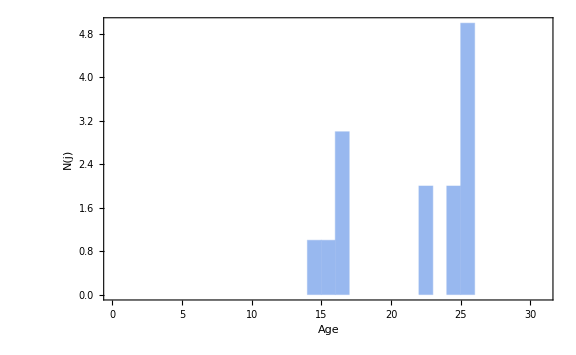

```mathematica
Histogram[NpT,{0,np+5,1},Frame->True,
LabelStyle->Directive[Black,25],FrameLabel->{Style["Age",24],Style["N(j)",24]},
ImageSize->Large]
```

```mathematica
P14=Nbin[[14]]/Ntotal
P15=Nbin[[15]]/Ntotal
P16=Nbin[[16]]/Ntotal
```

1/14

1/14

3/14

```mathematica
En general:
```

```mathematica
Pj=Range[1,np];(* An array *)
Do[Pj[[i]]=Nbin[[i]]/Ntotal;,{i,1,np}]
Pj[[22]]
```

1/7

```mathematica
En particular, la suma de todas las probabilidades es 1. "Seguro que tienes que tener alguna edad":
```

```mathematica
Sum[Pj[[i]], {i, 1, np}]
```

```mathematica
1
```

```mathematica
(* == Nice .. printing the sum itself *)
(* For the Average *)
sAve[n_Integer?Positive]:=Row[Table[k* Pj[[k]],{k,1,n}],"+"]
```

```mathematica
sAve[np]
```

++0000000000000115/1424/70000022/7024/7125/140

```mathematica
¿Cuál es la edad media (o media)? Respuesta:
```

```mathematica
Sum[i Pj[[i]], {i, 1, np}]
```

```mathematica
En general
```

```mathematica
jAve = Sum[j Pj[[j]], {j, 1, np}]
```

∑_(j=1)^np1 j Pj⟦j⟧

El valor esperado:

〈J〉 =∑_(j = 0)^∞ j P(j)                    (1.7)

```mathematica
¿Cuál es el promedio del cuadrado?
```

```mathematica
Sum[(i^2)  Pj[[i]], {i, 1, np}]
```

```mathematica
En general, el valor promedio de alguna función de j viene dado por
```

〈f(j)〉 =∑_(j = 0)^∞ f(j)* P(j).      (1.9)

```mathematica
Cuidado: la media del cuadrado, ⟨ j^2⟩, no es igual, en general, al cuadrado de la media, ⟨ j ⟩^2.
```

```mathematica
Necesitamos una medida numérica de la cantidad de "spread" en una distribución, con respecto al promedio. Las más obvias:
```

Δj=j-⟨j⟩

Y calcule el promedio

〈Δj〉=∑_(j = 0)^∞ (j - 〈j〉)* P(j)
=⟨j⟩-⟨j⟩=0!

En su lugar, el cuadrado antes de promediar:

σ^2=⟨(Δj)^2⟩.     (1.11)

```mathematica
La cantidad se conoce como la varianza de la distribución; con lo que se denomina desviación estándar
```

σ^2=⟨j^2⟩-⟨j⟩^2

```mathematica
Tomando la raíz cuadrada,
```

σ=√(⟨j^2⟩-⟨j⟩^2).     (1.12)

◀ prev - + prox ▶

e Guardar
d Resetear

## Variables continuas

```mathematica
Lo único sensato de lo que se puede hablar es de la probabilidad de que su edad se encuentre en algún intervalo, digamos entre los 16 y los 17 años.
```

Con la densidad de probabilidad ρ(x) [PDF], la probabilidad de que x se encuentre entre a y b viene dada por la integral de ρ(x):

Pab=∫_a^b ρ(x)ⅆx     (1.15)

1=∫_(-∞)^(+∞) ρ(x)ⅆx     (1.16)

⟨x⟩=∫_(-∞)^(+∞) x ρ(x)ⅆx     (1.17)

⟨f(x)⟩=∫_(-∞)^(+∞) f(x) ρ(x)ⅆx     (1.18)

σ^2=⟨(Δx)^2⟩ =⟨x^2⟩-⟨x⟩^2.     (1.19)

```mathematica
Ejemplo 1.1
```

```mathematica
xt=1/2 g t^2;
(* Solve for t *)
tx=Solve[xt==x,t][[2]]
```

{t→(√2 √x)/(√g)}

```mathematica
(* == The Velocity == *)
vt=D[xt,t];
Echo[vt, "Esta es la velocidad: "]
(* == Total Flight time ==*)
hT=1/2 g T2^2;
(* == Time is only positive ==*)
T1a=Reduce[hT==h &&T2>0&&g>0,T2,Reals];
T1=T1a[[3,2]];
Echo[T1,"Despejamos el tiempo total de vuelo: "]
(* == The Probability that the camera flashes in the interval dT is ==*)
(* dT/T1 , so the probability that photograph shows a distance in the
corresponding range dx is *)
(* dt = dx/v , I take it from above *)
PDFdx=dx/vt/T1/.tx;
Echo[PDFdx,"Escribirmos dt en funcion de x: "]

(* == In Mathematica factor out ==*)
PDF1=FullSimplify[Collect[PDFdx,dx]/dx];
Echo[PDF1, "Imprimimos el PDF: "]
```

Esta es la velocidad:   g t

g t

Despejamos el tiempo total de vuelo:   √2 √(h/g)

√2 √(h/g)

Escribirmos dt en funcion de x:   dx/(2 √g √(h/g) √x)

dx/(2 √g √(h/g) √x)

Imprimimos el PDF:   1/(2 √g √(h/g) √x)

1/(2 √g √(h/g) √x)

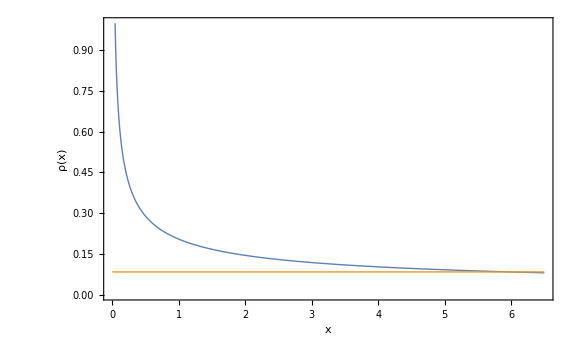

```mathematica
Plot[{PDF1/.{h->6,g->10.0},1/(2*6)},{x,0,6.5},
PlotStyle->Thick,PlotRange->{{0.,6.5},{0,1}},
Frame->True,
LabelStyle->Directive[Black,18],FrameLabel->{Style["x",24],Style["ρ(x)",24],Style["Fig 1.6: La probabilidad de densidad del Ex. 1.1",20]},ImageSize->Large]
```

```mathematica
Veamos algunas cosas
```

```mathematica
Integrate[PDF1 /. {h -> 6, g -> 10.}, {x, 0, 6}]
```

1.

```mathematica
El promedio
```

```mathematica
Avex1 = Integrate[x PDF1 /. {h -> 6, g -> 10.}, {x, 0, 6}]
```

2.

Mira h/3 !, algo menos que h/2 como se anticipó. La PDF puede ser infinita, pero la integral debe ser finita, de hecho menor o igual que 1.

◀ prev - + prox ▶

e Guardar
d Resetear

Normalización

```mathematica
Volvemos a la interpretación estadística de la función de onda.
La partícula tiene que estar en alguna parte:
```

∫_(-∞)^(+∞) |Ψ(x,t)|^2 ⅆx=1     (1.20)

Sin esto, la interpretación estadística no tendría sentido!!! ....

La clave para normalizar es darse cuenta de que si Ψ(x,t) es una solución de 1.1, entonces AΨ(x,t) también es una solución.

```mathematica
¡Espera!, supongamos que tengo la función de onda normalizada en t=0. ¿Cómo sé que se normalizará a medida que pase el tiempo y Ψ(x,t) evolucione?
```

Afortunadamente, la ecuación de Schrödinger tiene la notable propiedad de que preserva automáticamente la normalización de la función de onda: sin esta característica crucial, la ecuación de Schrödinger sería incompatible con la interpretación estadística, ¡y toda la teoría se desmoronaría!

d/dt∫_(-∞)^(+∞)|Ψ(x,t)|^2 ⅆx=ⅈℏ/(2m)(Ψ^*(∂Ψ)/(∂x)-(∂Ψ^*)/(∂x)Ψ)|+∞
-∞     (1.26)

Pero Ψ debe ir a cero más rápido que su derivada a medida que x -> (±) ∞ -- ¡De lo contrario, la función de onda no sería normalizable! Así que

d/dt∫_(-∞)^(+∞)|Ψ(x,t)|^2 ⅆx=0

◀ prev - + prox ▶

e Guardar
d Resetear

## Cuentas para llegar a (1.26), página anterior:

```mathematica
Clear[Ψ];
```

### La integral se puede escribir

```mathematica
Integrate[Abs[Ψ[x,t]]^2,x]==Integrate[Ψ[x,t] SuperStar[Ψ][x,t],x]
```

∫Abs[Ψ[x,t]]^2 ⅆx==∫Ψ[x,t] Ψ^*[x,t]ⅆx

### La Derivada entra en la integral y se puede escribir

```mathematica
Echo[D[(Ψ[x,t]*SuperStar[Ψ][x,t]),t],"Código Mathematica: "];
Echo[pdConv[D[(Ψ[x,t]*SuperStar[Ψ][x,t]),t]],"Escrito tradicional: "];
```

Código Mathematica:   Ψ^*[x,t] Ψ^(0,1)[x,t]+Ψ[x,t] (Ψ^*)^(0,1)[x,t]

Escrito tradicional:   Ψ(x,t) (∂Ψ^*(x,t))/(∂t)+Ψ^*(x,t) (∂Ψ(x,t))/(∂t)

### Las ecuaciones de Schrödinger se pueden escribir

```mathematica
TDSE=(ⅈ*ℏ)*D[Ψ[x,t],t]==hamiltonian[V[x,t]]@Ψ[x,t]
SuperStar[TDSE]=(-ⅈ*ℏ)*D[SuperStar[Ψ][x,t],t]==hamiltonian[V[x,t]]@SuperStar[Ψ][x,t]
```

ⅈ ℏ Ψ^(0,1)[x,t]==V[x,t] Ψ[x,t]-(ℏ^2 Ψ^(2,0)[x,t])/(2 m)

-ⅈ ℏ (Ψ^*)^(0,1)[x,t]==V[x,t] Ψ^*[x,t]-(ℏ^2 (Ψ^*)^(2,0)[x,t])/(2 m)

```mathematica
TDSEsol=Solve[TDSE,D[Ψ[x,t],t]][[1]][[1]];
SuperStar[TDSEsol]=Solve[SuperStar[TDSE],D[SuperStar[Ψ][x,t],t]][[1]][[1]];
```

```mathematica
Echo[I2=D[(Ψ[x,t]*SuperStar[Ψ][x,t]),t]/.{TDSEsol, SuperStar[TDSEsol]}//FullSimplify,"Código Mathematica: "];
Echo[pdConv[I2],"Escrito tradicional: "];
```

Código Mathematica:   (ⅈ ℏ (Ψ^*[x,t] Ψ^(2,0)[x,t]-Ψ[x,t] (Ψ^*)^(2,0)[x,t]))/(2 m)

Escrito tradicional:   (ⅈ ℏ (Ψ^*(x,t) (∂^2 Ψ(x,t))/(∂x^2)-Ψ(x,t) (∂^2 Ψ^*(x,t))/(∂x^2)))/(2 m)

```mathematica
Echo[TraditionalForm[1/(2*m)]*FullSimplify[(2*m)*Integrate[I2,x]],"Código Mathematica: "];
Echo[pdConv[TraditionalForm[1/(2*m)]*FullSimplify[(2*m)*Integrate[I2,x]]],"Escrito tradicional: "];
```

Código Mathematica:   ⅈ ℏ 1/(2 m) (Ψ^*[x,t] Ψ^(1,0)[x,t]-Ψ[x,t] (Ψ^*)^(1,0)[x,t])

Escrito tradicional:   ⅈ 1/(2 m) ℏ (Ψ^*(x,t) (∂Ψ(x,t))/(∂x)-Ψ(x,t) (∂Ψ^*(x,t))/(∂x))

◀ prev - + prox ▶

e Guardar
d Resetear

Momento

```mathematica
Para una partícula en estado Ψ, el valor esperado de x es
```

⟨x⟩=∫_(-∞)^(+∞) x |Ψ(x,t)|^2 ⅆx     (1.28)

```mathematica
El valor esperado es el promedio de mediciones repetidas en un conjunto de sistemas preparados de manera idéntica, no el promedio de mediciones repetidas en un mismo sistema.
```

```mathematica
〈x〉 cambia debido a Ψ(x,t), ¿queremos saber qué tan rápido?
```

(d⟨x⟩)/dt=∫x∂/(∂t)|Ψ|^2 dx=
ⅈℏ/(2m)∫x∂/(∂x)(Ψ^*(∂Ψ)/(∂x)-(∂Ψ^*)/(∂x)Ψ)dx   (1.29)

La regla del producto dice que

```mathematica
Prod1 = D[f[x] g[x], x]
```

g[x] f'[x]+f[x] g'[x]

si f[x] → x

```mathematica
D[x* g[x], x]
```

g[x]+x g'[x]

### Es decir que:

```mathematica
x*pdConv[D[g[x], x]]==pdConv[Inactivate[D[x* g[x], x]]]-g[x]
```

x (∂g(x))/(∂x)==-g[x]+(∂(x×g[x]))/(∂x)

### Integrando en ambos costados:

```mathematica
Integrate[x*D[g[x],x],x]==Integrate[D[x* g[x], x],x]-Integrate[g[x],x]
```

∫x g'[x]ⅆx==x g[x]-∫g[x]ⅆx

(d⟨x⟩)/dt=-ⅈℏ/(2m)∫(Ψ^*(∂Ψ)/(∂x)-(∂Ψ^*)/(∂x)Ψ)dx  (1.30)

```mathematica
Otra integración por partes
```

(d⟨x⟩)/dt=-ⅈℏ/m∫Ψ^*(∂Ψ)/(∂x)dx   (1.31)

```mathematica
D[(Ψ[x,t] SuperStar[Ψ][x,t]), x]
```

Ψ^*[x,t] Ψ^(1,0)[x,t]+Ψ[x,t] (Ψ^*)^(1,0)[x,t]

### Es decir que:

```mathematica
SuperStar[Ψ][x,t]*pdConv[D[Ψ[x,t],x]]==pdConv[Inactive[D[(Ψ[x,t] SuperStar[Ψ][x,t]), x]]-Ψ[x,t]*D[SuperStar[Ψ][x,t],x]]
```

(∂Ψ(x,t))/(∂x) Ψ^*[x,t]==Inactive[(∂(Ψ(x,t) Ψ^*(x,t)))/(∂x)]-Ψ(x,t) (∂Ψ^*(x,t))/(∂x)

### Integrando en ambos costados:

```mathematica
pdConv[Integrate[SuperStar[Ψ][x,t]*D[Ψ[x,t],x],x]]==pdConv[Integrate[D[(Ψ[x,t] SuperStar[Ψ][x,t]), x],x]-Integrate[Ψ[x,t]*D[SuperStar[Ψ][x,t],x],x]]
```

∫Ψ^*(x,t) (∂Ψ(x,t))/(∂x)ⅆx==Ψ(x,t) Ψ^*(x,t)-∫Ψ(x,t) (∂Ψ^*(x,t))/(∂x)ⅆx

```mathematica
Para nuestros propósitos bastará con postular que el valor esperado de la velocidad es igual a la derivada temporal del valor esperado de la posición:
```

⟨v⟩ =(d⟨x⟩)/dt    (1.32)

Es habitual trabajar con el momento lineal (p = mv), en lugar de la velocidad

⟨p⟩ =m(d⟨x⟩)/dt=-ⅈℏ∫Ψ^*(∂Ψ)/(∂x)dx(1.33)

```mathematica
Forma más sugerente
```

⟨x⟩ =∫ Ψ^*(x)Ψ dx,      (1.34)
⟨p⟩ =∫ Ψ^*(ℏ/ⅈ∂/(∂x))Ψ dx.      (1.35)

```mathematica
Para calcular el valor esperado de cualquiera de estas cantidades, Q(x, p):
```

⟨Q(x, p)⟩=∫ Ψ^*Q(x,ℏ/ⅈ∂/(∂x))Ψ dx.    (1.36)

◀ prev - + prox ▶

e Guardar
d Resetear

El principio de incertidumbre

Ahora bien, la longitud de onda de Ψ está relacionada con el momento de la partícula mediante la fórmula de Broglie:

```mathematica
p = (2πħ)/λ          (1.39)
```

Por lo tanto, una dispersión en la longitud de onda corresponde a una dispersión en el momento.

σ_x σ_p≥ℏ/2   (1.40)

```mathematica
donde Subscript[σ, x] es la desviación estándar en x, y Subscript[σ, p] es la desviación estándar en p. Este es el famoso principio de incertidumbre de Heisenberg.
```

◀ prev - + prox ▶

e Guardar
d Resetear

## Capítulo 2: Ecuación de Schrödinger independiente del tiempo

◀ prev - + prox ▶

e Guardar
d Resetear

Estados estacionarios

```mathematica
¡Deja de procrastinar! ... ¿Cómo se obtiene ψ(x,t) en primer lugar? Necesitamos resolver la ecuación de Schrödinger,
```

ⅈℏ(∂Ψ)/(∂t)=-ℏ^2/(2m)(∂^2 Ψ)/(∂x^2)+VΨ    (2.1)

```mathematica
para un potencial especificado V(x, t). En este capítulo asumimos que V es independiente de t. 
Método de separación de variables, buscamos soluciones que sean productos sencillos:
```

Ψ(x,t)=ψ(x)φ(t)  (2.2)

#### La ecuación de Schrödinger la escribimos:

```mathematica
SchroXT=ⅈ ℏ pdConv[D[Ψ[x,t],t]]==TraditionalForm[-ℏ^2/(2m)]pdConv[D[Ψ[x,t],{x,2}]]+V[x,t] Ψ[x,t]
```

ⅈ ℏ (∂Ψ(x,t))/(∂t)==-ℏ^2/(2 m) (∂^2 Ψ(x,t))/(∂x^2)+V[x,t] Ψ[x,t]

```mathematica
(* === Separation !! == Un poco de notación Mathematica == *)
Sep1={Ψ[x,t]->ψ[x]φ[t]}
(* == Dividing by psi phi *)
SchroX=(SchroXT/.Sep1)/(ψ[x]φ[t])
```

{Ψ[x,t]→φ[t] ψ[x]}

1/(φ[t] ψ[x])(ⅈ ℏ (∂(φ(t) ψ(x)))/(∂t)==-ℏ^2/(2 m) (∂^2 (φ(t) ψ(x)))/(∂x^2)+V[x,t] φ[t] ψ[x])

ⅈℏ 1/φ dφ/dt=-ℏ^2/(2m)1/ψ(d^2 ψ)/dx^2+V    (2.3)

La única forma en que esto puede ser cierto es si ambos lados son de hecho constantes: ¡piensa!

ⅈℏ dφ/dt=φE,    (2.4)

-ℏ^2/(2m)(d^2 ψ)/dx^2+Vψ=Eψ    (2.5)

Dos ecuaciones diferenciales ordinarias.

```mathematica
DSolve[D[φ[t],t]==-(ⅈ/ℏ) (Ener) φ[t],φ[t],t][[1]][[1]]
```

φ[t]→ⅇ^(-(ⅈ Ener t)/ℏ) C[1]

φ=Exp(-ⅈEt/ℏ),    (2.6)

El segundo se llama la 
ecuación de Schrödinger independiente del tiempo; no podemos ir más allá hasta que se especifique el potencial V(x).

1. Son estados estacionarios. La densidad de probabilidad no depende del tiempo. Cada valor esperado es constante en el tiempo.

⟨Q(x, p)⟩ = ∫ ψ^*Q(x,ℏ/ⅈ∂/(∂x))ψ dx.     (2.9)

En particular, 〈x〉 es constante, y 〈p〉= 0. Nada sucede en un estado estacionario.

2. Son estados de energía total definida. El operador hamiltoniano correspondiente, obtenido por la sustitución canónica p → ℏ/ⅈ∂/(∂x) , es, por lo tanto,

Ĥ=-ℏ^2/(2m)∂^2/(∂x^2)+V(x)    (2.11)

La ecuación de Schrödinger independiente del tiempo
[ T.I.S.E ]

Ĥ ψ=Eψ    (2.12)
⟨H⟩ = E  (2.13)

⟨H^2⟩  =  E^2 ; entonces

σ_H^2= ⟨H^2⟩ - ⟨H⟩^2=0!    (2.14)

Conclusión: Una solución separable tiene la propiedad de que cada medición de la energía total devolverá con certeza el valor E.

Ψ(x,t)=∑_(n=1)^∞ c_n ψ_n(x)Exp(-ⅈE_nt/ℏ).    (2.15)

```mathematica
3. La solución general es una combinación lineal de soluciones separables.
```

```mathematica
El punto es que una vez que hayas resuelto la ecuación independiente del tiempo, ¡esencialmente estarás listo!
```

◀ prev - + prox ▶

e Guardar
d Resetear

## Ejercicios

Practicar:

```mathematica
hamiltonian[V0]@(E^(I k x))//Collect[#,E^(I k x)]&
```

ⅇ^(ⅈ k x) (V0+(k^2 ℏ^2)/(2 m))

```mathematica
Entonces esa onda plana es una función propia del hamiltoniano con V0 (partícula libre).
```

```mathematica
(* Esto es para decir que es un operador linear ==*)
hamiltonian[V]@(a f[x] +b g[x])==a hamiltonian[V]@f[x]+b hamiltonian[V]@g[x]//Expand
```

True

```mathematica
La ecuación dependiente del tiempo
```

```mathematica
I ℏ D[Ψ[x, t], t] == hamiltonian[V][Ψ[x, t]]
```

ⅈ ℏ Ψ^(0,1)[x,t]==V Ψ[x,t]-(ℏ^2 Ψ^(2,0)[x,t])/(2 m)

```mathematica
La ecuación independiente del tiempo
```

```mathematica
hamiltonian[V][ψ[x]] == Ener ψ[x]
```

V ψ[x]-(ℏ^2 ψ''[x])/(2 m)==Ener ψ[x]

```mathematica
Así que vamos a trabajar con
```

```mathematica
schroedingerD[V[x]][ψ[x]] == 0
```

-Ener ψ[x]+V[x] ψ[x]-(ℏ^2 ψ''[x])/(2 m)==0

◀ prev - + prox ▶

e Guardar
d Resetear

El Pozo del Cuadrado Infinito

```mathematica
Suponer
```

V(x)={0, si  0≤x≤a
∞, de otra forma

```mathematica
(* == Define the limits here == *)
myCero1=0.1;
mya1=3.;
myPotWall1=Piecewise[{{0,myCero1<x<a},{Infinity,x>a}}]
```

Piecewise[{{0, 0.1<x<a}, {∞, x>a}, {0, True}}]

◀ prev - + prox ▶

e Guardar
d Resetear

## Representación gráfica de la Figura 2.1:

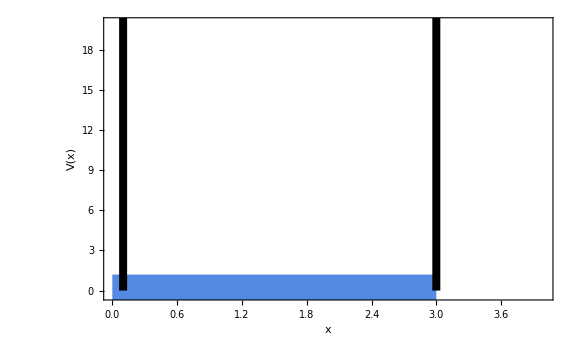

```mathematica
Plot[myPotWall1/.{a->mya1},{x,0,4},
PlotRange->{{0.,4},{-0.3,20}},
Frame->True,
PlotStyle->{Thickness@0.04},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.01,
Line[{{myCero1,0},{myCero1,36}}],Line[{{mya1,0},{mya1,36}}]},
(* ====================== *)
LabelStyle->Directive[Black,25],
FrameLabel->{Style["x",24],Style["V(x)",24],Style["Fig 2.1: El potencial  cuadrado infinito",20]},
FrameTicks->None,ImageSize->Large]
```

Dentro del pozo V=0, la ecuación de Schrödinger independiente del tiempo es la siguiente:

(d^2 ψ)/dx^2=-k^2ψ    (2.21)
donde k^2=(2mE)/ℏ

La ecuación (2.21) es la ecuación clásica del oscilador armónico simple; La solución general es

ψ(x)=Asin(kx)+Bcos(kx)   (2.22)

La continuidad de ψ requiere que

ψ(0)=ψ(a)=0   (2.23)
B=0, y por lo tanto

ψ(x)=A sin(kx)    (2.24)

```mathematica
Solución no trivial, sin(kx)=0; lo que significa
```

```mathematica
ka = 0, ±π, ±2π, ±3π, ...     (2.25)
```

Las distintas soluciones son:

```mathematica
Subscript[k, n]=nπ/a,con n=1,2,3,.... (2.26)
```

```mathematica
Curiosamente, la condición de contorno en x = a no determina la constante A, sino la constante k, y por lo tanto los posibles valores de E:
```

```mathematica
Subscript[E, n]=(ℏ^2(Subscript[k, n])^2)/(2m)=(n^2 π^2 ℏ^2)/(2m a^2),con n=1,2,3,.... (2.27)
```

```mathematica
En contraste radical con el caso clásico, una partícula cuántica en el pozo cuadrado infinito  no puede tener cualquier energía que desee. Tiene que ser uno de estos valores especiales permitidos.
```

Para encontrar A, normalizamos ψ.

```mathematica
I1=Integrate[(A^2*(Sin[(k*x)])^2),{x,0,a}]==1
```

-(A^2 (-2 a k+Sin[2 a k]))/(4 k)==1

```mathematica
I1/.{k->(5)π/a}
```

(a A^2)/2==1

```mathematica
Solve[I1/.{k->(5)π/a}, A]
```

{{A→-(√2)/(√a)},{A→(√2)/(√a)}}

```mathematica
Las soluciones son:
```

ψ_n(x)=√(2/a)sin(nπ/a x)   (2.28)

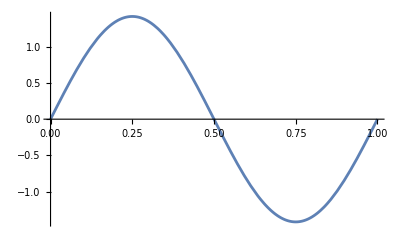

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
(* == Analitically == *)
Plot[√(2/a)Sin[n π x / a]/.{n->2,a->1.},{x,0,1}]
```

## AutoFunción de la TISE

```mathematica
1. CONFIGURACIÓN
```

```mathematica
Remove["Global`*"]
```

```mathematica
phi[n_,x_]:=Sqrt[2/a]Sin[n Pi x / a]
```

```mathematica
(* First we see that this is solution if == *)
E2SolveInf1=schroedingerD[0]@phi[n,x]/phi[n,x]==0//ExpandAll
```

-Energy+(n^2 π^2 ℏ^2)/(2 a^2 m)==0

```mathematica
e[n_] = Energy /. Solve[E2SolveInf1, Energy][[1]]
```

(n^2 π^2 ℏ^2)/(2 a^2 m)

```mathematica
e[2] /. {ℏ -> 1., m -> 1., a -> 1}
```

19.7392

Numéricamente

```mathematica
myEqWell1 = schroedingerD[0][phi[x]] == 0 /. {ℏ -> 1, m -> 1}
```

-Energy phi[x]-phi''[x]/2==0

```mathematica
¡Súper solución! Juega...
```

```mathematica
myEqWell2 = ParametricNDSolve[{schroedingerD[0][phi[x]] == 0, phi[0] == 0, phi'[0] == 1} /. {ℏ -> 1, m -> 1, Energy -> e[n] /. {ℏ -> 1., m -> 1., a -> 1}, a -> 1}, phi, {x, 0, 1.1}, {n}]
```

{phi→ParametricFunction[<>]}

◀ prev - + prox ▶

e Guardar
d Resetear

## Representación gráfica de la Figura 2.2:

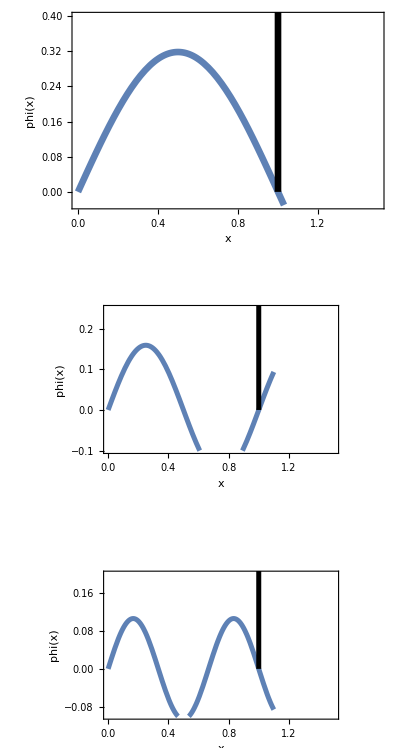

```mathematica
plWell1=Plot[phi[1][x]/.myEqWell2,{x,0,1.1},
PlotRange->{{0.,1.5},{-0.03,0.4}},
Frame->True,
PlotStyle->{Thickness@0.01},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.01,
Line[{{1.,0},{1.,3}}]},
(* ====================== *)
LabelStyle->Directive[Black,20],
FrameLabel->{Style["x",20],Style["phi(x)",20],
Style["Fig. 2.2: The first three stationary
states of the infinite square well"]},
FrameTicks->None,
ImageSize->478];
(* == Sol n=2 *)
plWell2=Plot[phi[2][x]/.myEqWell2,{x,0,1.1},
PlotRange->{{0.,1.5},{-0.1,0.25}},
Frame->True,
PlotStyle->{Thickness@0.01},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.01,
Line[{{1.,0},{1.,3}}]},
(* ====================== *)
LabelStyle->Directive[Black,20],
FrameLabel->{Style["x",20],Style["phi(x)",20]},
FrameTicks->None,ImageSize->Medium];
(* == Sol n=3 *)
plWell3=Plot[phi[3][x]/.myEqWell2,{x,0,1.1},
PlotRange->{{0.,1.5},{-0.1,0.2}},
Frame->True,
PlotStyle->{Thickness@0.01},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.01,
Line[{{1.,0},{1.,3}}]},
(* ====================== *)
LabelStyle->Directive[Black,20],
FrameLabel->{Style["x",20],Style["phi(x)",20]},
FrameTicks->None,ImageSize->Medium];
(* == Combining Plots ==*)
GraphicsGrid[{{plWell1},{plWell2},{plWell3}},Background->LightGray]
```

```mathematica
n=1 se denomina estado fundamental, los demás se denominan estados excitados.
```

```mathematica
Propiedades importantes:
```

1. Se alteran pares e impares, con respecto al centro del pozo:
El ψ_1 es par El ψ_2 es impar, el ψ_3 es par, y así sucesivamente.

2. A medida que aumenta su energía, cada estado sucesivo tiene un nodo de modo. El ψ_1 no tiene ninguno, el ψ_2 tiene uno, el ψ_3 tiene dos, y así sucesivamente.

3. Son mutuamente ortogonales, en el sentido de que

... trabajando un poco en (2.29)

De hecho, podemos combinar la ortogonalidad y la normalización en una sola afirmación:

∫(ψ_m(x))^*ψ_n(x)dx=δ_mn,    (2.30)

```mathematica
donde Subscript[δ, mn] (el llamado delta de Kronecker) se define de la manera habitual,
```

δ_mn={0, if m≠n
1, if m=n       (2.31)

```mathematica
Decimos que los ψ son ortonormales.
```

```mathematica
4. Son completas, en el sentido de que cualquier otra función, f(x), puede expresarse como una combinación lineal de ellas:
```

f(x)=∑_(n = 1)^∞ c_n ψ_n(x)=Sqrt[2/a]∑_(n = 1)^∞ c_n sin(nπ/a x)
(2.32)

```mathematica
Los coeficientes se pueden evaluar con el truco de Fourier
```

c_n=∫(ψ_m(x))^*f(x)dx=δ_mn,    (2.34)

```mathematica
Estas propiedades son extremadamente poderosas y generales.
```

```mathematica
La solución más general:
```

Ψ(x,t)=∑_(n=1)^∞ c_n √(2/a)sin(nπ/a x)Exp[(-i n^2 π^2 ℏ^2/2 ma^2)t].   (2.36)

```mathematica
Y los coeficientes
```

c_n=√(2/a)∫_0^a sin(nπ/a x)Ψ(x,0)ⅆx   (2.37)

Dada la función de onda inicial, Ψ(x,0), primero calculamos los coeficientes de expansión c_n, usando (2.37), y luego los conectamos a la ecuación (2.36) para obtener Ψ(x,t). Armados con la función de onda, estamos en condiciones de calcular cualquier cantidad dinámica de interés, utilizando el procedimiento del Capítulo 1. Y este mismo ritual se aplica a cualquier potencial: las únicas cosas que cambian son la forma funcional de los ψ y la ecuación de las energías permitidas.

```mathematica
myASol22=Integrate[x^2(a-x)^2,{x,0,a}]
```

a^5/30

```mathematica
(* == The nth coefficient is Eq. 2.37 ==*)
mySol22a=Simplify[Sqrt[2/a]*Integrate[Sin[n Pi/a x]Sqrt[1/myASol22] x(a-x),{x,0,a}],a>0]
```

-(2 √15 (-2+2 Cos[n π]+n π Sin[n π]))/(n^3 π^3)

```mathematica
mySol22a /. {n -> 1}
```

(8 √15)/π^3

```mathematica
Qué |Subscript[c, n]|^2 indica la probabilidad de que una medición de la energía produzca el valor Subscript[E, n].
```

```mathematica
Por supuesto, la suma de estas probabilidades debe ser 1,
```

```mathematica
∑_(n = 1)^∞ |Subscript[c, n]|^2=1       (2.38)
```

Además, el valor esperado de la energía debe ser

<H> =∑_(n=1)^∞ |c_n|^2 E_n  (2.39)

```mathematica
La probabilidad de obtener una energía determinada es independiente del tiempo, por lo que el valor de H. Esta es una manifestación de la conservación de la energía en la mecánica cuántica.
```

◀ prev - + prox ▶

e Guardar
d Resetear

## Ejemplo 2.3 (aula)

```mathematica
Problema 2.3
Problema 2.4
```

◀ prev - + prox ▶

e Guardar
d Resetear

El oscilador armónico

```mathematica
El paradigma de un oscilador armónico clásico es una masa m unida a un resorte de constante de fuerza k. La moción se rige por la ley de Hooke,
```

```mathematica
F=-kx=m(d^2 x)/dt^2
```

```mathematica
(ignorando la fricción), y la solución es
```

x(t)=A sen(ω t)+B cos(ω t),

```mathematica
donde ω = Sqrt[k/m] es la frecuencia (angular) de oscilación. La energía potencial es
```

V(x)=1/2 kx^2 (2.42)

Su gráfico es una parábola.

◀ prev - + prox ▶

e Guardar
d Resetear

## Para representar la Figura 2.4

```mathematica
Vx = - 1/2 k (x - x0)^2  + V0
```

V0+1/2 k (x-x0)^2

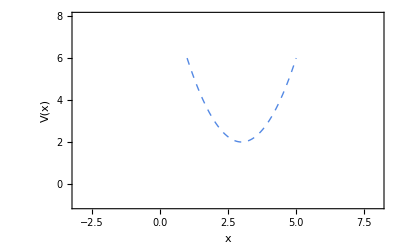

```mathematica
plFig24a = Plot[Vx /. {k -> 2., x0 -> 3., V0 -> 2.}, {x, 1, 5}, PlotRange -> {{-3, 8}, {-1, 8}}, PlotStyle -> {Thick, Dashed}, Frame -> True, LabelStyle -> Directive[Black, 25], FrameLabel -> {"x", "V(x)"}, FrameTicks -> None]
```

Pero prácticamente cualquier potencial es aproximadamente parabólico, en la vecindad del mínimo local (fig. 2.4). Formalmente, si expandimos V(x) en una serie de Taylor aproximadamente el mínimo:

```mathematica
fx=1/2x^2+Exp[-x^2/4]*Sin[3 x]+5.
```

5.+x^2/2+ⅇ^(-x^2/4) Sin[3 x]

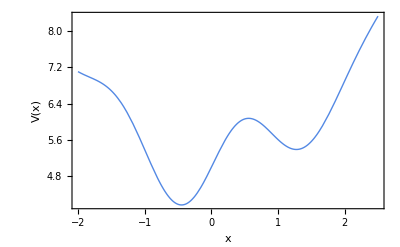

```mathematica
plFig24b = Plot[fx, {x, -2, 2.5}, PlotStyle -> {Thick}, Frame -> True, LabelStyle -> Directive[Black, 25], FrameLabel -> {"x", "V(x)", "Fig. 2.4: Aproximacion Parabolica"}, FrameTicks -> None]
```

```mathematica
myTaylor24a = Normal[Series[fx, {x, 1.2, 2}]]
```

5.41126-0.4917 (-1.2+x)+3.03709 (-1.2+x)^2

```mathematica
plFig24c = Plot[myTaylor24a, {x, -2, 2.5}, PlotStyle -> {Thick, Dashed}, Frame -> True, LabelStyle -> Directive[Black, 25], FrameLabel -> {"x", "V(x)"}, FrameTicks -> None];
```

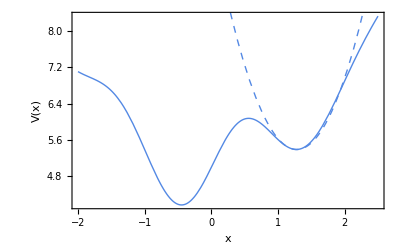

```mathematica
Show[{plFig24b, plFig24c}]
```

```mathematica
Series[V[x], {x, x0, 3}]
```

V[x0]+V'[x0] (x-x0)+1/2 V''[x0] (x-x0)^2+1/6 V^(3)[x0] (x-x0)^3+O[x-x0]^4

V(x)≃1/2 V'' (x0) (x-x0)^2,

que describe un oscilador armónico simple (aproximadamente x0), con una constante de resorte efectiva k = V''(x0).  Prácticamente cualquier movimiento oscilatorio es aproximadamente armónico simple siempre que la amplitud sea pequeña.

```mathematica
El problema cuántico consiste en resolver la ecuación de Schrödinger para el potencial:
```

V(x) = 1/2 mω^2 x^2    (2.43)

```mathematica
Basta con resolver la ecuación de Schrödinger independiente del tiempo:
```

-ℏ^2/(2m)(d^2 ψ)/dx^2+1/2 m ω^2 x^2=E ψ .  (2.44)

```mathematica
1. Método de la serie de potencias. 2. Operadores de escaleras.
```

◀ prev - + prox ▶

e Guardar
d Resetear